Let’s do 3D and find what Px,Py, Pz should be, then we can compare the bulk contribution analytically and numerically.

```mathematica
F[T_,Px_,Py_,Pz_,α1,α12,α111,α112,α123]:=α1((Px^2+Py^2+Pz^2)+α12/α1(Px^2 Py^2+Py^2 Pz^2 + Px^2 Pz^2)+α111/α1(Px^6+Py^6+Py^6)+α112/α1(Px^4(Py^2+Pz^2)+Py^4(Pz^2+Px^2)+Pz^4(Px^2+Py^2))+α123/α1(Px^2 Py^2 Pz^2))
```

```mathematica
F[T_,Px_,Py_,Pz_,α1_,α12_,α111_,α112_,α123_]:=α1((Px^2+Py^2+Pz^2)+α12/α1(Px^2 Py^2+Py^2 Pz^2 + Px^2 Pz^2)+α111/α1(Px^6+Py^6+Pz^6)+α112/α1(Px^4(Py^2+Pz^2)+Py^4(Pz^2+Px^2)+Pz^4(Px^2+Py^2))+α123/α1(Px^2 Py^2 Pz^2))
```

```mathematica
{sol=Solve[{D[F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,2.6*10^8,6.1*10^8,-3.7*10^9],Px]==0,D[F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,2.6*10^8,6.1*10^8,-3.7*10^9],Py]==0,D[F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,2.6*10^8,6.1*10^8,-3.7*10^9],Pz]==0,D[D[F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,2.6*10^8,6.1*10^8,-3.7*10^9],Px],Px]>0,D[D[F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,2.6*10^8,6.1*10^8,-3.7*10^9],Py],Py]>0,D[D[F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,2.6*10^8,6.1*10^8,-3.7*10^9],Pz],Pz]>0},{Px,Py,Pz}],Dimensions[sol]}
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{{Px→-0.685782,Py→0,Pz→0},{Px→-0.383184,Py→-0.383184,Pz→-0.124509},{Px→-0.383184,Py→-0.383184,Pz→0.124509},{Px→-0.383184,Py→-0.124509,Pz→-0.383184},{Px→-0.383184,Py→-0.124509,Pz→0.383184},{Px→-0.383184,Py→0.124509,Pz→-0.383184},{Px→-0.383184,Py→0.124509,Pz→0.383184},{Px→-0.383184,Py→0.383184,Pz→-0.124509},{Px→-0.383184,Py→0.383184,Pz→0.124509},{Px→-0.330359,Py→-0.330359,Pz→-0.330359},{Px→-0.330359,Py→-0.330359,Pz→0.330359},{Px→-0.330359,Py→0.330359,Pz→-0.330359},{Px→-0.330359,Py→0.330359,Pz→0.330359},{Px→-0.124509,Py→-0.383184,Pz→-0.383184},{Px→-0.124509,Py→-0.383184,Pz→0.383184},{Px→-0.124509,Py→0.383184,Pz→-0.383184},{Px→-0.124509,Py→0.383184,Pz→0.383184},{Px→0,Py→-0.685782,Pz→0},{Px→0,Py→0,Pz→-0.685782},{Px→0,Py→0,Pz→0.685782},{Px→0,Py→0.685782,Pz→0},{Px→0.124509,Py→-0.383184,Pz→-0.383184},{Px→0.124509,Py→-0.383184,Pz→0.383184},{Px→0.124509,Py→0.383184,Pz→-0.383184},{Px→0.124509,Py→0.383184,Pz→0.383184},{Px→0.330359,Py→-0.330359,Pz→-0.330359},{Px→0.330359,Py→-0.330359,Pz→0.330359},{Px→0.330359,Py→0.330359,Pz→-0.330359},{Px→0.330359,Py→0.330359,Pz→0.330359},{Px→0.383184,Py→-0.383184,Pz→-0.124509},{Px→0.383184,Py→-0.383184,Pz→0.124509},{Px→0.383184,Py→-0.124509,Pz→-0.383184},{Px→0.383184,Py→-0.124509,Pz→0.383184},{Px→0.383184,Py→0.124509,Pz→-0.383184},{Px→0.383184,Py→0.124509,Pz→0.383184},{Px→0.383184,Py→0.383184,Pz→-0.124509},{Px→0.383184,Py→0.383184,Pz→0.124509},{Px→0.685782,Py→0,Pz→0}},{38,3}}

```mathematica
(0.3831839969194138^2+0.3831839969194138^2+0.1245090294328103^2)^(1/2)
```

0.556024

```mathematica
((-0.38838580999327166)^2+0.38838580999327166^2)^(1/2)
```

0.54926

There are quite a few minimums here.

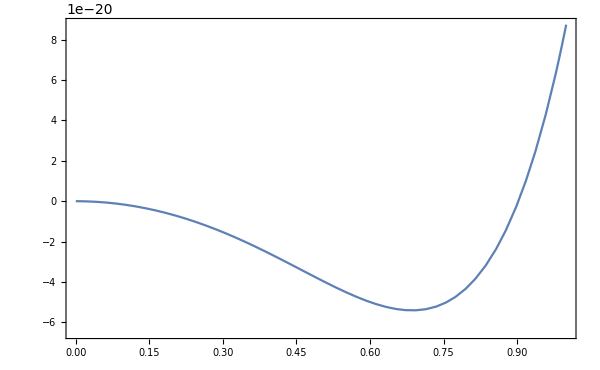
{-Graphics-,{{Px→0.685782}}}

```mathematica
{Plot[(1*10^-9)^3 F[0,Px,0,0,-1.7252*10^8,7.5*10^8,2.6*10^8,6.1*10^8,-3.7*10^9],{Px,0,1},ImageSize->600,Frame->True,AxesOrigin->{0,-6.5*10^-20}],Solve[{D[F[0,Px,0,0,-1.7252*10^8,7.5*10^8,2.6*10^8,6.1*10^8,-3.7*10^9],Px]==0,Px>0},Px]}
```

toss out 6th order, → ~ error of 6-9% on values of P_j ✓ directions are right,✓

 make sure field aligns, 
 
  turn electrostatics on, 
  
  then try domain

try large domain terms with 6th order.

Fourth order:

```mathematica
{sol=Solve[{D[F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,0,0,0],Px]==0,D[F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,0,0,0],Py]==0,D[F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,0,0,0],Pz]==0,D[D[F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,0,0,0],Pz],Pz]==0},{Px,Py,Pz}],Dimensions[sol]}
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{{Px→-0.339136,Py→-0.339136,Pz→-0.339136},{Px→-0.339136,Py→-0.339136,Pz→0.339136},{Px→-0.339136,Py→0.339136,Pz→-0.339136},{Px→-0.339136,Py→0.339136,Pz→0.339136},{Px→0.,Py→-0.479611,Pz→-0.479611},{Px→0.,Py→-0.479611,Pz→0.479611},{Px→0.,Py→0.479611,Pz→-0.479611},{Px→0.,Py→0.479611,Pz→0.479611},{Px→0.339136,Py→-0.339136,Pz→-0.339136},{Px→0.339136,Py→-0.339136,Pz→0.339136},{Px→0.339136,Py→0.339136,Pz→-0.339136},{Px→0.339136,Py→0.339136,Pz→0.339136},{Px→-0.479611,Py→0.,Pz→-0.479611},{Px→-0.479611,Py→0.,Pz→0.479611},{Px→0.479611,Py→0.,Pz→-0.479611},{Px→0.479611,Py→0.,Pz→0.479611}},{16,3}}

```mathematica
(.479-.532)/(.532)
```

-0.0996241

```mathematica
(.35-.33)/(.33)
```

0.0606061

Applied field, fourth order, let Ez = 1*10^4, Ey = Ex = 0. A strong enough field will show the changes and verify that 1.) the polarization aligns and 2.) the numbers we get are indeed correct:

```mathematica
Solve[{D[((10^-9)^3 F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,0,0,0]-Pz Ez),Px]==0,D[((10^-9)^3 F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,0,0,0]-Pz Ez),Py]==0,
D[((10^-9)^3 F[T,Px,Py,Pz,-1.7252*10^8,7.5*10^8,0,0,0]-Pz Ez),Pz]==0,Pz>0},{Px,Py,Pz}]/.Ez->5*10^-19
```

$Aborted

```mathematica
{Manipulate[Plot3D[(10^-9)^3 F[0,0,Px,Pz,-1.7252*10^8,7.5*10^8,0,0,0]-Pz Ez,{Pz,-2,2},{Px,-2,2}],{Ez,0,10^-19}],F[0,0,0,Pz,-1.7252*10^8,7.5*10^8,0,0,0]-Pz Ez}
```

{,-Ez Pz-1.7252×10^8 (0.+Pz^2)}

Note the values of Py and Px and how they are different from the above set of solutions.

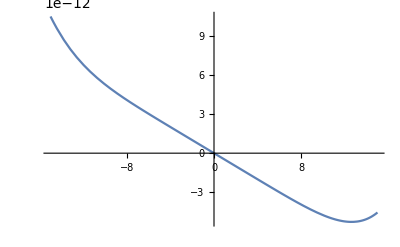

```mathematica
Plot[(10^-9)^3 F[0,0,0,Pz,-1.7252*10^8,7.5*10^8,2.6*10^8,6.1*10^8,-3.7*10^9]-(10^-9)^2 Pz Ez/.{Ez->5*10^5},{Pz,-15,15}]
```

Interestingly enough, the solution must be around -4e-19 for 5e-19 electric field. Can check to see if P and F match for given input fields in Moose.

```mathematica
Solve[D[(10^-9)^3 F[0,0,0,Pz,-1.7252*10^8,7.5*10^8,2.6*10^8,6.1*10^8,-3.7*10^9]-(10^-9)^2 Pz 5*10^10,Pz]==0,Pz]
```

{{Pz→-102.124-74.1972 ⅈ},{Pz→-102.124+74.1972 ⅈ},{Pz→39.0078-120.054 ⅈ},{Pz→39.0078+120.054 ⅈ},{Pz→126.232}}

```mathematica
(10^-9)^3 F[0,0,0,Pz,-1.7252*10^8,7.5*10^8,2.6*10^8,6.1*10^8,-3.7*10^9]-(10^-9)^2 Pz 5*10^10/.Pz->126.23188899964053
```

-5.25966×10^-6

```mathematica
Solve[(10^-9)^3 F[0,0,0,Pz,-1.7252*10^8,7.5*10^8,2.6*10^8,6.1*10^8,-3.7*10^9]-(10^-9)^2 Pz 5*10^10==2.844*10^-21,Pz]
```

{{Pz→-146.136-106.174 ⅈ},{Pz→-146.136+106.174 ⅈ},{Pz→-5.688×10^-14},{Pz→55.819-171.793 ⅈ},{Pz→55.819+171.793 ⅈ},{Pz→180.634}}